# Solving x-Space RGEs of Track Functions Numerically: The Moment Method

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/liirba/Desktop/draft_x-space/evo_MomentMethod

```mathematica
(* We use the renormalization group equations of up to nmax-th moments of track functions. nmax≤28 is required due to the NLO evolution equations of the track function moments we have in the directory EvolutionEquations4Moments/ . *)
nmax:=28
```

## α_s(μ)

```mathematica
betafunction={β0-> (11 ca)/3-(4 tf nf)/3,
β1-> 34/3 ca^2-20/3 ca tf nf-4 cf tf nf,
β2-> (158/27 ca+44/9 cf) nf^2 tf^2+(-205/9 ca cf-1415/27 ca^2+2 cf^2) nf tf+2857/54 ca^3,β3->1093/729 nf^3+(50065/162+6472/81 Zeta[3]) nf^2+(-1078361/162-6508/27 Zeta[3]) nf+3564 Zeta[3]+149753/6}/.{nf->Nf,ca->CA,cf->CF,tf->TF};
```

```mathematica
colorfactor={Nf->5,CA->3,CF->4/3,TF->1/2};
```

```mathematica
alphas[mu_]:=Module[{ll},(4 Pi)/β0*(1/ll-β1/(β0^2 ll^2) Log[ll]+β1^2/(β0^4 ll^3) (Log[ll]^2-Log[ll]-1)+β2/(β0^3 ll^3)+β1^3/(β0^6 ll^4) (-Log[ll]^3+5/2 Log[ll]^2+2 Log[ll]-1/2)-3 (β1 β2)/(β0^5 ll^4) Log[ll]+β3/(2 β0^4 ll^4))/.ll->Log[mu^2/(213/1000)^2]/.betafunction/.colorfactor];
```

```mathematica
alphas[10]//N[#,200]&
```

0.17927784197950593970782556625434294730631124811398790077047796986886243234213856259707746848581962196582961984434474711014445302800420286202617393181767327817548000635709792377612875464520906856386741

## RGEs for T_i(n) (i=q,g)

### RHS of the order-a_s evolution equations of track function moments, with generic n

```mathematica
(*quark*)
DT[0,q,n_]:=3 CF T[q,n]+CF(  (4/n-(2 (3+n))/((1+n)(2+n)))T[g,n]+(-4 HarmonicNumber[n]-(2 (3+2 n))/((1+n)(2+n)))T[q,n]+Sum[T[q,k]T[g,n-k] Binomial[n,k]((4 Gamma[1+k] Gamma[-k+n])/Gamma[1+n]-(2 (3+k+n) Gamma[1+k] Gamma[1-k+n])/Gamma[3+n]),{k,1,n-1}]  )//Collect[#,{T[_,_],Nf,TF,CA,CF},Expand]&;
```

```mathematica
(*gluon*)
DT[0,g,n_]:=((11 CA)/3-(4 Nf TF)/3) T[g,n]+  (-(2 CA (-6+n^2 (3+n)))/(n (1+n) (2+n) (3+n))-2 CA HarmonicNumber[n]+2 CA (-2/(1+n)+1/(2+n)-1/(3+n))-2 CA (EulerGamma+PolyGamma[0,n]))T[g,n]+Sum[T[g,k]T[g,n-k] Binomial[n,k](2 CA Gamma[k] (1/Gamma[n]+(k (k-n) (11+k^2-k n+n (9+2 n)))/Gamma[4+n]) Gamma[-k+n]),{k,1,n-1}] +sumq Sum[T[q,k]T[qbar,n-k] Binomial[n,k](1/Gamma[4+n] 2 (4+2 k^2-2 k n+n (3+n)) TF Gamma[1+k] Gamma[1-k+n]),{k,0,n}] /.T[p_,0]->1 //Collect[#,{sumq,T[_,_],Nf,TF,CA,CF},Expand]&;
```

### RHS of the order-a_s^2 evolution equations for the first nmax moments

```mathematica
(*gluon*)
Table[DT[1,g,iii]=(<<("EvolutionEquations4Moments/kernels_gluon/gluon_n"<>ToString[iii]<>"_ana.m"))/.{tt->T,fq->sumq,fQ->sumQ},{iii,1,nmax}];
```

```mathematica
(*quark*)
Table[DT[1,q,iii]=(<<("EvolutionEquations4Moments/kernels_quark/quark_n"<>ToString[iii]<>"_ana.m"))/.{tt->T,fq->sumq,fQ->sumQ},{iii,1,nmax}];
```

## Processing...

```mathematica
(*For simplicity, here we assume all (anti-)quark flavors have the same track function.*)
```

### order-a_s

```mathematica
kklist[0,g]=Table[DT[0,g,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

```mathematica
kklist[0,q]=Table[DT[0,q,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

### order-a_s^2

```mathematica
kklist[1,g]=Table[DT[1,g,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

```mathematica
kklist[1,q]=Table[DT[1,q,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

## Evolution

```mathematica
(* Here, we present a simple way to numerically solve the evolution equations for the moments. Of course, one can choose their favorite programs such as Julia and Matlab to do that more efficiently. *)
```

### up to order- a_s

```mathematica
evoLO::usage="evoLO[initialT, initialmu, finalmu, steps, digitprecision] is for the LO evolution, requiring as the first argument the initial track function moments (a list with as first entry an array of gluon and as second entry an array of quark track function moments), as the second and third arguments the initial and final scales, as the fourth argument the number of steps, and as the last argument the working precision. The Runge–Kutta fourth-order method is applied. With more steps, higher accuracy of the numerical solutions of the moments can be achieved. ";
```

```mathematica
evoLO[initialT_,initmu_,finalmu_,steps_,digitprecision_]:=Module[{lmu=Log[initmu],stepsize=(Log[finalmu]-Log[initmu])/steps,asvalue,ii,ttnew,grad},
(* the initial condition for the moments *)
Table[tt[g,ii]=initialT⟦1,ii⟧;tt[q,ii]=initialT⟦2,ii⟧,{ii,1,nmax}];
(*evolving...*)
Monitor[Do[
(*1*)
asvalue=alphas[initmu*E^((rr-1)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,1]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>tt[p,n])//N[#,digitprecision]&;
grad[q,1]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>tt[p,n])//N[#,digitprecision]&;
(*2*)
asvalue=alphas[initmu*E^((rr-1/2)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,2]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//N[#,digitprecision]&;
grad[q,2]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//N[#,digitprecision]&;
(*3*)
grad[g,3]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//N[#,digitprecision]&;
grad[q,3]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//N[#,digitprecision]&;
(*4*)
asvalue=alphas[initmu*E^(rr*stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,4]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//N[#,digitprecision]&;
grad[q,4]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//N[#,digitprecision]&;
(*final*)
Table[tt[g,ii]=tt[g,ii]+1/6*stepsize*(grad[g,1]⟦ii⟧+2 grad[g,2]⟦ii⟧+2 grad[g,3]⟦ii⟧+grad[g,4]⟦ii⟧)//N[#,digitprecision]&;
tt[q,ii]=tt[q,ii]+1/6*stepsize*(grad[q,1]⟦ii⟧+2 grad[q,2]⟦ii⟧+2 grad[q,3]⟦ii⟧+grad[q,4]⟦ii⟧)//N[#,digitprecision]&,{ii,1,nmax}]
,{rr,1,steps}],ProgressIndicator[rr,{1,steps}]];
{Table[tt[g,ii],{ii,1,nmax}],Table[tt[q,ii],{ii,1,nmax}]}
]
```

### up to order- a_s^2

```mathematica
evoNLO::usage="evoNLO[initialT, initialmu, finalmu, steps, digitprecision] is for the evolution up to NLO, requiring as the first argument the initial track function moments (a list with as first entry an array of gluon and as second entry an array of quark track function moments), as the second and third arguments the initial and final scales, as the fourth argument the number of steps, and as the last argument the working precision. The Runge–Kutta fourth-order method is applied. With more steps, higher accuracy of the numerical solutions of the moments can be achieved. ";
```

```mathematica
evoNLO[initialT_,initmu_,finalmu_,steps_,digitprecision_]:=Module[{lmu=Log[initmu],stepsize=(Log[finalmu]-Log[initmu])/steps,asvalue,ii,ttnew,grad},
(* the initial condition for the moments *)
Table[tt[g,ii]=initialT⟦1,ii⟧;tt[q,ii]=initialT⟦2,ii⟧,{ii,1,nmax}];
(*evolving...*)
Monitor[Do[
(*1*)
asvalue=alphas[initmu*E^((rr-1)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,1]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>tt[p,n])//Expand;
grad[q,1]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>tt[p,n])//Expand;
(*2*)
asvalue=alphas[initmu*E^((rr-1/2)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,2]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//Expand;
grad[q,2]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//Expand;
(*3*)
grad[g,3]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//Expand;
grad[q,3]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//Expand;
(*4*)
asvalue=alphas[initmu*E^(rr*stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,4]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//Expand;
grad[q,4]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//Expand;
(*final*)
Table[tt[g,ii]=tt[g,ii]+1/6*stepsize*(grad[g,1]⟦ii⟧+2 grad[g,2]⟦ii⟧+2 grad[g,3]⟦ii⟧+grad[g,4]⟦ii⟧)//Expand;
tt[q,ii]=tt[q,ii]+1/6*stepsize*(grad[q,1]⟦ii⟧+2 grad[q,2]⟦ii⟧+2 grad[q,3]⟦ii⟧+grad[q,4]⟦ii⟧)//Expand,{ii,1,nmax}]
,{rr,1,steps}],ProgressIndicator[rr,{1,steps}]];
{Table[tt[g,ii],{ii,1,nmax}],Table[tt[q,ii],{ii,1,nmax}]}
]
```

# Examples

## Initial condition: Toy model

### Initial Conditions: μ_0=10 GeV, toy model

#### To get the initial moments

```mathematica
μ0=10;
```

```mathematica
trackfunction["LO","g",μ0]=12 x^2(1-x);
```

```mathematica
trackfunction["LO","q",μ0]=12 x^2(1-x);
```

```mathematica
temp1=Table[Integrate[trackfunction["LO","g",μ0]*x^ii,{x,0,1}],{ii,1,nmax}]
```

{3/5,2/5,2/7,3/14,1/6,2/15,6/55,1/11,1/13,6/91,2/35,1/20,3/68,2/51,2/57,3/95,1/35,2/77,6/253,1/46,1/50,6/325,2/117,1/63,3/203,2/145,2/155,3/248}

```mathematica
temp2=Table[Integrate[trackfunction["LO","q",μ0]*x^ii,{x,0,1}],{ii,1,nmax}]
```

{3/5,2/5,2/7,3/14,1/6,2/15,6/55,1/11,1/13,6/91,2/35,1/20,3/68,2/51,2/57,3/95,1/35,2/77,6/253,1/46,1/50,6/325,2/117,1/63,3/203,2/145,2/155,3/248}

```mathematica
initialT={(*gluon*)temp1,(*quark*)temp2};
```

```mathematica
Clear[temp1,tempg,tempq,temp2]
```

### Polynomial basis

```mathematica
(* mnum is the number of the moments that we use to restore T(x)'s, including the zeroth moment *)
(* the degree of the polynomial is mnum-1 *)
```

```mathematica
(* the polynomial basis we choose*)
basis[mnum_]:=Table[{Sum[mnum^2/(i+j-1)If[i>1,Product[1-mnum^2/(k-1)^2,{k,2,i}],1]If[j>1,Product[1-mnum^2/(k-1)^2,{k,2,j}],1] x^(j-1),{j,1,mnum}]},{i,1,mnum}];
```

### Evolving moments and restoring T(x) from the moments: LO

```mathematica
?evoLO
```

#### μ=100 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=100;
```

```mathematica
(* evolving... *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,10,100,100,200];
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,μ0,mu1,100,200];
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

### Evolving moments and restoring T(x) from the moments: NLO

```mathematica
?evoNLO
```

#### μ=100 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=100;
```

```mathematica
(* evolving... *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,100,200];
```

```mathematica
(*25 moments*)
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,100,200];
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

### Plots

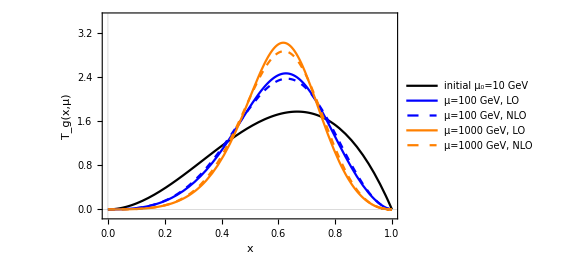

```mathematica
plotT[g]=Plot[{trackfunction["LO","g",μ0],poly["LO",g,100,25],poly["NLO",g,100,25],poly["LO",g,1000,25],poly["NLO",g,1000,25]},{x,0,1},PlotRange->{{0,1},{-0.1,3.5}},PlotStyle->{{Black},{Blue},{Blue,Dashed},{Orange},{Orange,Dashed}},PlotTheme->"Scientific",FrameLabel->{{"T_g(x,μ)",None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},PlotLegends->Placed[{"initial μ_0=10 GeV","μ=100 GeV, LO","μ=100 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```

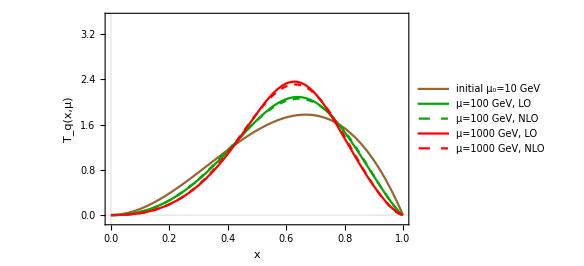

```mathematica
plotT[q]=Plot[{trackfunction["LO","q",μ0],poly["LO",q,100,25],poly["NLO",q,100,25],poly["LO",q,1000,25],poly["NLO",q,1000,25]},{x,0,1},PlotRange->{{0,1},{-0.1,3.5}},PlotStyle->{{Brown},{Darker[Green]},{Darker[Green],Dashed},{Red},{Red,Dashed}},PlotTheme->"Scientific",FrameLabel->{{"T_q(x,μ)",None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},PlotLegends->Placed[{"initial μ_0=10 GeV","μ=100 GeV, LO","μ=100 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```

## Initial condition: NLO track functions (from Pythia)

### Initial Conditions: μ_0=100 GeV, from Pythia

```mathematica
<<"trackfunctions_mu_100GeV_fromPythia.m";
```

#### To get the initial moments

```mathematica
(* We approximate the data extracted from Pythia, listed in "trackfunctions_mu_100GeV_fromPythia.m", with polynomials. The comparison of our polynomials and the approximate functions obtained by the Mathematica function "BSplineFunction" is shown in the plot below in this subsubsection. *)
```

```mathematica
(*
Here, we suggest that the expression of the initial track function T(x) be in terms of x and exact numbers (such as integers and fractions), since numbers without sufficiently high precision lead to the uncertainties in the values of the moments T(n) and then with such errors the polynomial restored from those moment values are likely to further degenerate even at the initial scale. Additionally, with the exact numbers it would be convenient to set arbitrarily high working precision for the evolution process. 
*)
```

```mathematica
μ0:=100
```

```mathematica
trackfunction["NLO","g",μ0]=(200200000000000000000 (1-x) x (21419474266211533/50000000000000000-(4600195813799859 x)/500000000000000+(7209602286141799 x^2)/10000000000000000+(607618412717947 x^3)/625000000000-(1049070507133021 x^4)/125000000000+(3918006898250861 x^5)/100000000000-(12313170345048283 x^6)/100000000000+(1386807755230999 x^7)/5000000000-(4214918390951007 x^8)/10000000000+(786706194158069 x^9)/2000000000-(2499420132205481 x^10)/12500000000+(4210582649382423 x^11)/100000000000))/200431366434915776521;
```

```mathematica
trackfunction["NLO","q",μ0]=(90090000000000000000 (1-x) x (5269472300270851/5000000000000000-(3565441155520761 x)/125000000000000+(218906629876317 x^2)/312500000000-(2001886526509999 x^3)/250000000000+(5424007460990269 x^4)/100000000000-(11518813211585241 x^5)/50000000000+(6383004178141191 x^6)/10000000000-(11680671441913843 x^7)/10000000000+(279889949239983 x^8)/200000000-(2642120757682381 x^9)/2500000000+(45690411986243253 x^10)/100000000000-(8625915422473433 x^11)/100000000000))/89985178346857411693;
```

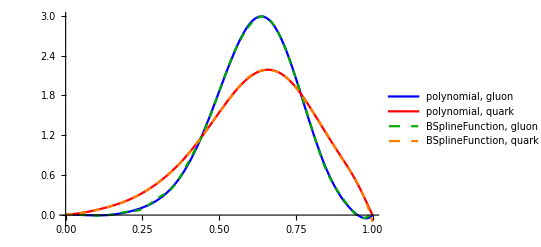

```mathematica
Plot[{trackfunction["NLO","g",μ0],trackfunction["NLO","q",μ0],trackNLO[6][x],(Plus@@(trackNLO[#][x]&/@Range[5]))/5},{x,0,1},PlotStyle->{{Blue},{Red},{Darker[Green],Dashed},{Orange,Dashed}},PlotLegends->{"polynomial, gluon","polynomial, quark","BSplineFunction, gluon","BSplineFunction, quark"}]
```

```mathematica
tempg=Table[Integrate[trackfunction["NLO","g",μ0]*x^ii,{x,0,1}],{ii,1,nmax}];
```

```mathematica
tempq=Table[Integrate[trackfunction["NLO","q",μ0]*x^ii,{x,0,1}],{ii,1,nmax}];
```

```mathematica
initialT={(*gluon*)tempg,(*quark*)tempq};
```

```mathematica
Clear[temp1,tempg,tempq,temp2]
```

### Polynomial basis

```mathematica
(* mnum is the number of the moments that we use to restore T(x), including the zeroth moment *)
(* the degree of the polynomial is mnum-1 *)
```

```mathematica
(* the polynomial basis we choose*)
basis[mnum_]:=Table[{Sum[mnum^2/(i+j-1)If[i>1,Product[1-mnum^2/(k-1)^2,{k,2,i}],1]If[j>1,Product[1-mnum^2/(k-1)^2,{k,2,j}],1] x^(j-1),{j,1,mnum}]},{i,1,mnum}];
```

### Evolving moments and restoring T(x) from the moments: LO

```mathematica
?evoLO
```

#### μ=10 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=10;
```

```mathematica
(* evolving... *)
(* For the plots in the papers we used 30000 steps, but it's acceptable to use fewer steps such as 100 or 1000 steps. *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,μ0,mu1,1000,200];
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
(* For the plots in the papers we used 30000 steps, but it's acceptable to use fewer steps such as 100 or 1000 steps. *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,μ0,mu1,1000,200];
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

### Evolving moments and restoring T(x) from the moments: NLO

```mathematica
?evoNLO
```

#### μ=10 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=10;
```

```mathematica
(* evolving... *)
(* For the plots in the papers we used 30000 steps, but it's acceptable to use fewer steps such as 100 or 1000 steps. *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,1000,200];
```

```mathematica
(*25 moments*)
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
(* For the plots in the papers we used 30000 steps, but it's acceptable to use fewer steps such as 100 or 1000 steps. *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,1000,200];
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

### Plots

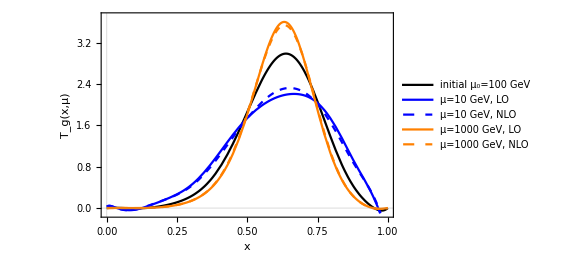

```mathematica
plotT[g]=Plot[{trackfunction["NLO","g",μ0],poly["LO",g,10,25],poly["NLO",g,10,25],poly["LO",g,1000,25],poly["NLO",g,1000,25]},{x,0,1},PlotRange->{{0,1},{-0.1,3.7}},PlotStyle->{{Black},{Blue},{Blue,Dashed},{Orange},{Orange,Dashed}},PlotTheme->"Scientific",FrameLabel->{{Style["T_g(x,μ)",Italic],None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},WorkingPrecision->100,PlotLegends->Placed[{"initial μ_0=100 GeV","μ=10 GeV, LO","μ=10 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```

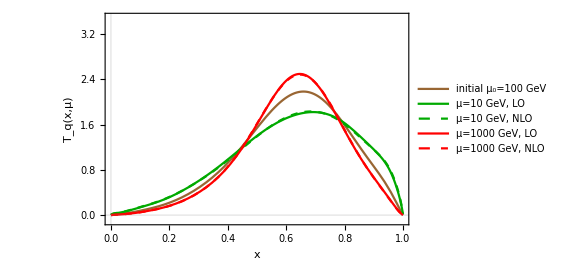

```mathematica
plotT[q]=Plot[{trackfunction["NLO","q",μ0],poly["LO",q,10,25],poly["NLO",q,10,25],poly["LO",q,1000,25],poly["NLO",q,1000,25]},{x,0,1},PlotRange->{{0,1},{-0.1,3.5}},PlotStyle->{{Brown},{Darker[Green]},{Darker[Green],Dashed},{Red},{Red,Dashed}},PlotTheme->"Scientific",FrameLabel->{{Style["T_q(x,μ)",Italic],None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},WorkingPrecision->100,PlotLegends->Placed[{"initial μ_0=100 GeV","μ=10 GeV, LO","μ=10 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```